```mathematica
Na=60;
Ls=3;
```

```mathematica
Pa=IntegerPartitions[Na,Ls];
lP=Length[Pa];
```

```mathematica
lPa=Table[Length[Pa[[j]]],{j,lP}];
```

```mathematica
t0={0,0};
```

```mathematica
fPa=Table[Join[Pa[[j]],t0],{j,lP}];
sPa=Table[fPa[[j]][[1;;3]],{j,lP}];
```

#### Particle conserved basis

```mathematica
Hbs=Flatten[Table[Permutations[sPa[[j]]],{j,lP}],1];
lH=Length[Hbs];
lHshouldbe=Binomial[Na+Ls-1,Na];
H3s=0*IdentityMatrix[lH];
```

```mathematica
lH
```

496

```mathematica
lHshouldbe
```

496

#### Hopping Hamiltonian

```mathematica
ApAm[m_,Hb_,Na_,lH_]:=For[j=1,j≤lH,j++,If[Hb[[j]][[m]]<Na && Hb[[j]][[m+1]]>0,H3s[[j]][[Position[Hb,ReplacePart[Hb[[j]],{m->(Hb[[j]][[m]]+1),(m+1)->(Hb[[j]][[m+1]]-1)}]][[1]]]]+=√((Hb[[j]][[m]]+1.0)(Hb[[j]][[m+1]]))]](*Subscript[a, m]^+Subscript[a, m+1]*)
```

```mathematica
ApAm[1,Hbs,Na,lH]
ApAm[2,Hbs,Na,lH]
```

```mathematica
MatrixForm[Hhop=(H3s+Transpose[H3s])];
```

#### onsite interaction

```mathematica
Honsite=1/Na *Table[If[j==k, (Hbs[[j]][[1]])^2+(Hbs[[j]][[2]])^2+(Hbs[[j]][[3]])^2,0],{j,lH},{k,lH}];(*U0/Na * (Subscript[n, 1] Subscript[n, 1]-Subscript[n, 2] Subscript[n, 2]+Subscript[n, 3] Subscript[n, 3])*)
```

#### Nearest-neighbor interaction

```mathematica
Hnn=2 1/Na *Table[If[j==k,-Hbs[[j]][[1]]*Hbs[[j]][[2]]-Hbs[[j]][[2]]*Hbs[[j]][[3]]+Hbs[[j]][[1]]*Hbs[[j]][[3]],0],{j,lH},{k,lH}];(*U1 * Subscript[n, m] Subscript[n, m+1]*)
```

#### Tilt potential

```mathematica
Htit=Table[If[j==k, (Hbs[[j]][[3]]-Hbs[[j]][[1]]),0],{j,lH},{k,lH}];(*U2 * Subscript[n, m] Subscript[n, m+2]*)
```

#### eigen energies

```mathematica
H0=1/(√2)Hhop+U0 Honsite+U1 Hnn;
```

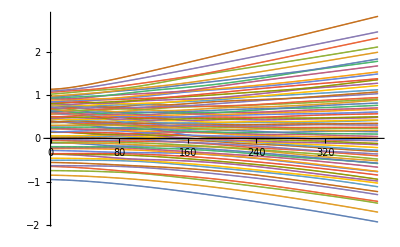

```mathematica
egall=Transpose[1/Na Table[Sort[Eigenvalues[(H0 + ep0 * Htit)/.{U0->0.7,U1->1.2}]],{ep0,0.1,2.0,0.005}]];
ListPlot[egall]
```

```mathematica
Dimensions[egall]
```

{66,381}

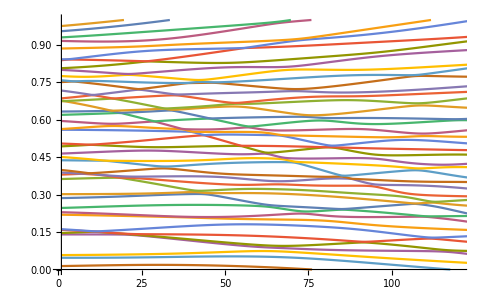

```mathematica
f1=ListPlot[egall,Joined->True,PlotRange->{{1,120},{0.0,1}}]
```

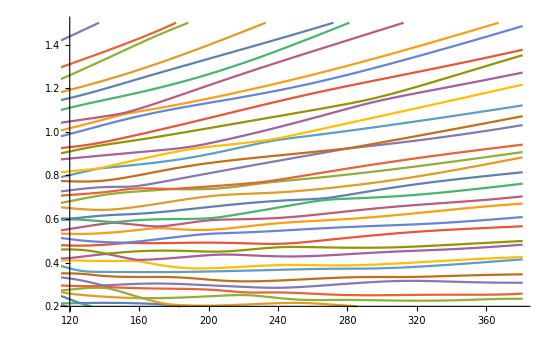

```mathematica
f2=ListPlot[egall,Joined->True,PlotRange->{{120,380},{0.2,1.5}}]
```

#### level properties in the chaotic regime

```mathematica
epsilon=1.9;
```

```mathematica
Htot0=(epsilon*Htit + Hhop+Honsite+Hnn)/.{U0->0.7,U1->1.2};
```

```mathematica
eeg0=Eigenvalues[Htot0];
evec0=Eigenvectors[Htot0];
```

#### Level spacing distribution

```mathematica
Esort=Sort[eeg0];
ratdrop  = 0.05* lH; (*drop 5% levels at the two edges*)
nhalf=Floor[ratdrop/2];
Ndstep =Floor[(lH-ratdrop)/5]; (*average every 5 levels*)
```

```mathematica
Do[emean = (Esort[[nhalf + 5 * j]] - Esort[[nhalf + 5 *(j-1)]])/5.0;
Do[espace[k]=(Esort[[nhalf + k]] - Esort[[(nhalf-1)+k]])/emean,{k,5 *(j-1),5j}],{j,Ndstep}];
```

```mathematica
(*setting the histogram for level spacing*)
dmin = 0.0;
dmax = 8.0;
bin = 0.1;
Nbin = IntegerPart[(dmax - dmin)/bin];
```

```mathematica
Do[xbin[j]=bin * (j-1),{j,Nbin}];
Do[Nenergy[j] = 0.0, {j,Nbin}];
```

```mathematica
Do[Do[If[xbin[j]≤espace[k]<xbin[j+1],Nenergy[j] = Nenergy[j]+1],{j,Nbin}],{k,10*Ndstep}](*generate the distributions*)
normbin = bin * Sum[Nenergy[j],{j,Nbin}];
Do[normNenergy[j]=Nenergy[j]/normbin,{j,Nbin}]
```

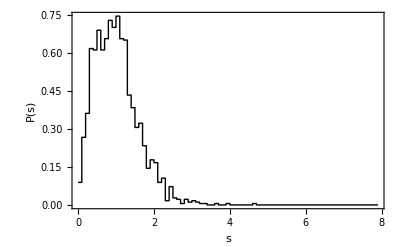

```mathematica
Ehist={};
k=0;
Do[k +=1;Ehist = Append[Ehist,{xbin[k],normNenergy[k]}];Ehist =Append[Ehist,{xbin[k+1],normNenergy[k]}],{j,Nbin-1}]
histPlot=ListPlot[Ehist,Joined->True,PlotStyle->{Black,Thick},LabelStyle->Directive[Bold,Medium],Frame->True,FrameLabel->{"s","P(s)"}]
```

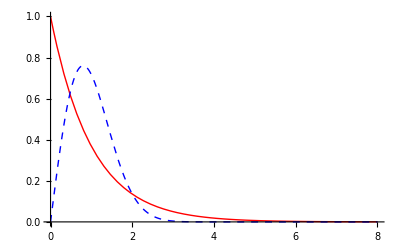

```mathematica
WignerDysonPossion=Plot[{Exp[-s],π s/2.0*Exp[-π s^2/4.0]},{s,0,8},PlotStyle->{{Red,Thick},{Blue,Thick,Dashed}},PlotRange->All]
```

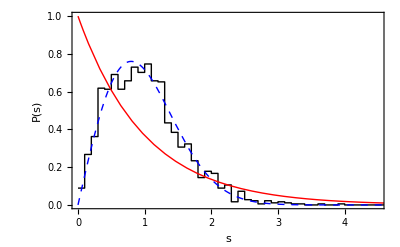

```mathematica
Show[histPlot,WignerDysonPossion,PlotRange->{{0,4.5},{0,1}}]
```

#### No. of principal components

```mathematica
Do[nPC[j]=1/Sum[Abs[evec0[[j,kk]]]^4,{kk,lH}],{j,lH}];
nPCdist=Table[{eeg0[[j]],nPC[j]},{j,lH}];
```

$Aborted

```mathematica
ListPlot[nPCdist,PlotRange->All,LabelStyle->Directive[Bold, Medium],Frame->True,FrameLabel->{"Energy","No. PC"}]
```